```mathematica
xsize=100;
ysize=100;
```

```mathematica
SetDirectory["C:/Users/colin/Dropbox/SC502/Winter2019/MeshProbs-MPI"]
```

C:\Users\colin\Dropbox\SC502\Winter2019\MeshProbs-MPI

```mathematica
dat2=ReadList["mysolution.txt",Number,RecordLists->True];
```

```mathematica
Dimensions[dat2]
```

{100,100}

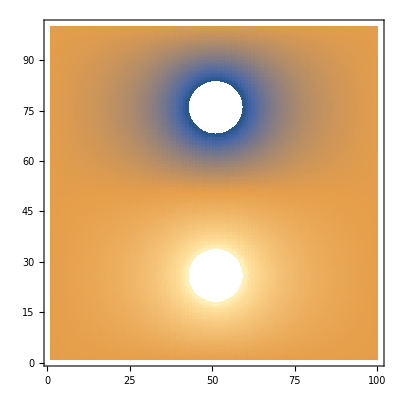

```mathematica
ListDensityPlot[dat2]
```

```mathematica
ListPlot3D[dat2,PlotRange->All]
```

-Graphics3D-

```mathematica
dat3=ReadList["Solution0.Txt",Number,RecordLists->True];dat4=ReadList["Solution1.Txt",Number,RecordLists->True];dat5=ReadList["Solution2.Txt",Number,RecordLists->True];dat6=ReadList["Solution3.Txt",Number,RecordLists->True];
```

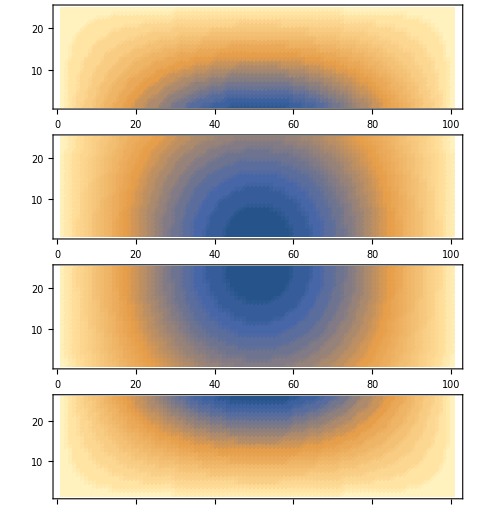

```mathematica
GraphicsColumn[{ ListDensityPlot[dat6,AspectRatio->Dimensions[dat6][[1]]/Dimensions[dat6][[2]]],ListDensityPlot[dat5,AspectRatio->Dimensions[dat5][[1]]/Dimensions[dat5][[2]]],ListDensityPlot[dat4,AspectRatio->Dimensions[dat4][[1]]/Dimensions[dat4][[2]]],ListDensityPlot[dat3,AspectRatio->Dimensions[dat3][[1]]/Dimensions[dat3][[2]]]}]
```

```mathematica
ListPlot3D[dat5,PlotRange->All,BoxRatios->{4,1,1}]
```

-Graphics3D-

```mathematica
dat0=ReadList["result0_0.txt",Number,RecordLists->True];dat1=ReadList["result0_1.txt",Number,RecordLists->True];dat2=ReadList["result0_2.txt",Number,RecordLists->True];dat3=ReadList["result1_0.txt",Number,RecordLists->True];
dat4=ReadList["result1_1.txt",Number,RecordLists->True];dat5=ReadList["result1_2.txt",Number,RecordLists->True];dat6=ReadList["result2_0.txt",Number,RecordLists->True];dat7=ReadList["result2_1.txt",Number,RecordLists->True];
dat8=ReadList["result2_2.txt",Number,RecordLists->True];
```

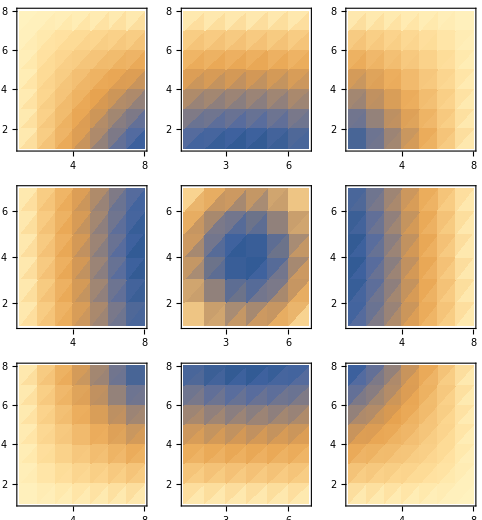

```mathematica
GraphicsGrid[{{ListDensityPlot[Transpose[dat6],AspectRatio->Dimensions[dat4][[1]]/Dimensions[dat4][[2]]],ListDensityPlot[Transpose[dat7],AspectRatio->Dimensions[dat3][[1]]/Dimensions[dat3][[2]]],ListDensityPlot[Transpose[dat8],AspectRatio->Dimensions[dat3][[1]]/Dimensions[dat3][[2]]]},{ListDensityPlot[Transpose[dat3],AspectRatio->Dimensions[dat3][[1]]/Dimensions[dat3][[2]]],ListDensityPlot[Transpose[dat4],AspectRatio->Dimensions[dat4][[1]]/Dimensions[dat4][[2]]],ListDensityPlot[Transpose[dat5],AspectRatio->Dimensions[dat3][[1]]/Dimensions[dat3][[2]]]},{ ListDensityPlot[Transpose[dat0],AspectRatio->Dimensions[dat6][[1]]/Dimensions[dat6][[2]]],ListDensityPlot[Transpose[dat1],AspectRatio->Dimensions[dat5][[1]]/Dimensions[dat5][[2]]],ListDensityPlot[Transpose[dat2],AspectRatio->Dimensions[dat4][[1]]/Dimensions[dat4][[2]]]}}]
```

```mathematica
dat2=BinaryReadList["output.bin",Table["Real64",{i,1,21}]];
```

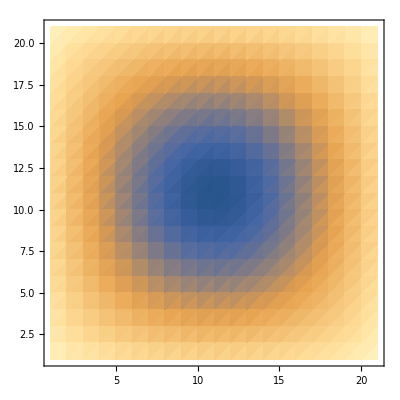

```mathematica
ListDensityPlot[dat2]
```

```mathematica
ListPlot3D[dat2,PlotRange->All]
```

-Graphics3D-